```mathematica
A=({{1, 3, 1, 0, 3, 10, a}, {2, 4, 0, 1, 6, -7, b}})
B=A//RowReduce
```

{{1,3,1,0,3,10,a},{2,4,0,1,6,-7,b}}

{{1,0,-2,3/2,3,-61/2,1/2 (-4 a+3 b)},{0,1,1,-1/2,0,27/2,a-b/2}}

```mathematica
A//TeXForm
```

\left(
\begin{array}{lllllll}
 1 & 3 & 1 & 0 & 3 & 10 & a \\
 2 & 4 & 0 & 1 & 6 & -7 & b
\end{array}
\right)

```mathematica
B//TeXForm
```

\left(
\begin{array}{lllllll}
 1 & 0 & -2 & \frac{3}{2} & 3 & -\frac{61}{2} & \frac{1}{2} (3 b-4 a) \\
 0 & 1 & 1 & -\frac{1}{2} & 0 & \frac{27}{2} & a-\frac{b}{2}
\end{array}
\right)

```mathematica
({{-2, 1, 0, 0}, {1, 0, 1, 0}, {0, 0, 0, 1}})
```

```mathematica
A=({{2, 1, 1}, {1, 2, 0}, {0, 0, 3}})
Eigenvalues[A]
Eigenvectors[A]
A//TeXForm
```

{{2,1,1},{1,2,0},{0,0,3}}

{3,3,1}

{{1,1,0},{0,0,0},{-1,1,0}}

\left(
\begin{array}{lll}
 2 & 1 & 1 \\
 1 & 2 & 0 \\
 0 & 0 & 3
\end{array}
\right)

```mathematica
A=({{13, 3}, {-7, 2}})
%//TeXForm
```

{{13,3},{-7,2}}

\left(
\begin{array}{ll}
 13 & 3 \\
 -7 & 2
\end{array}
\right)

```mathematica
Inverse[A]//TeXForm
```

\left(
\begin{array}{ll}
 \frac{2}{47} & -\frac{3}{47} \\
 \frac{7}{47} & \frac{13}{47}
\end{array}
\right)

```mathematica
A=({{2, 3}, {1, -2}})
B=({{1, 2}, {0, -1}})
AI=Inverse[A]
BI=Inverse[B]
```

{{2,3},{1,-2}}

{{1,2},{0,-1}}

{{2/7,3/7},{1/7,-2/7}}

{{1,2},{0,-1}}

```mathematica
TeXForm[BI]
```

\left(
\begin{array}{ll}
 1 & 2 \\
 0 & -1
\end{array}
\right)

```mathematica
TeXForm[BI.A.{-1,3}]
```

\{-7,7\}

```mathematica
TeXForm[AI]
```

\left(
\begin{array}{ll}
 \frac{2}{7} & \frac{3}{7} \\
 \frac{1}{7} & -\frac{2}{7}
\end{array}
\right)

```mathematica
TeXForm[AI.B.{-1,3}]
```

\left\{\frac{1}{7},\frac{11}{7}\right\}

```mathematica
TeXForm[B.{-1,3}]
```

\{5,-3\}

```mathematica
A=({{1, 1}, {1, -1}, {2, 3}})
Cc=({{1, 1, 3}, {0, 1, 2}, {0, 0, 1}})
B=({{2, -1}, {3, 1}})
```

{{1,1},{1,-1},{2,3}}

{{1,1,3},{0,1,2},{0,0,1}}

{{2,-1},{3,1}}

```mathematica
TeXForm[A]
```

\left(
\begin{array}{cc}
 1 & 1 \\
 1 & -1 \\
 2 & 3
\end{array}
\right)

```mathematica
TeXForm[B]
```

\left(
\begin{array}{cc}
 2 & -1 \\
 3 & 1
\end{array}
\right)

```mathematica
TeXForm[Cc]
```

\left(
\begin{array}{ccc}
 1 & 1 & 3 \\
 0 & 1 & 2 \\
 0 & 0 & 1
\end{array}
\right)

```mathematica
TeXForm[Inverse[Cc]]
```

\left(
\begin{array}{ccc}
 1 & -1 & -1 \\
 0 & 1 & -2 \\
 0 & 0 & 1
\end{array}
\right)

```mathematica
TeXForm[Inverse[C].A.B]
```

C^{-1}.\left(
\begin{array}{cc}
 5 & 0 \\
 -1 & -2 \\
 13 & 1
\end{array}
\right)

```mathematica
A=({{1, 1, -1}, {2, 3, 4}})
R=RowReduce[A]
```

{{1,1,-1},{2,3,4}}

{{1,0,-7},{0,1,6}}

```mathematica
NullSpace[A]
```

{{7,-6,1}}

```mathematica
TeXForm[A]
```

\left(
\begin{array}{ccc}
 1 & 1 & -1 \\
 2 & 3 & 4
\end{array}
\right)

```mathematica
TeXForm[R]
```

\left(
\begin{array}{ccc}
 1 & 0 & -7 \\
 0 & 1 & 6
\end{array}
\right)

```mathematica
B=({{7, 1, 0}, {-6, 0, 1}, {1, 0, 0}})
```

{{7,1,0},{-6,0,1},{1,0,0}}

```mathematica
TeXForm[A]
```

\left(
\begin{array}{cccc}
 7 & 1 & 0 & 0 \\
 -6 & 0 & 1 & 0 \\
 1 & 0 & 0 & 1
\end{array}
\right)

```mathematica
TeXForm[RowReduce[A]]
```

\left(
\begin{array}{cccc}
 1 & 0 & 0 & 1 \\
 0 & 1 & 0 & -7 \\
 0 & 0 & 1 & 6
\end{array}
\right)

```mathematica
A=({{1, 1, -1}, {2, 3, 4}})
B=({{7, 1, 0}, {-6, 0, 1}, {1, 0, 0}})
TeXForm[A.B]
```

{{1,1,-1},{2,3,4}}

{{7,1,0},{-6,0,1},{1,0,0}}

\left(
\begin{array}{ccc}
 0 & 1 & 1 \\
 0 & 2 & 3
\end{array}
\right)

```mathematica
A=({{1, 1, -1}, {2, 3, 4}})
B=({{1, 0, 7}, {0, 1, -6}, {0, 0, 1}})
Cc=({{1, 1}, {2, 3}})
TeXForm[Inverse[Cc].A.B]
```

{{1,1,-1},{2,3,4}}

{{1,0,7},{0,1,-6},{0,0,1}}

{{1,1},{2,3}}

\left(
\begin{array}{ccc}
 1 & 0 & 0 \\
 0 & 1 & 0
\end{array}
\right)

```mathematica
A=({{2, -1, 0, 0}, {0, 1, 1, 0}, {2, 0, 1, 0}, {1, 0, 0, 1}})
R=RowReduce[A]
NullSpace[A]
NA=({{-1, 1, 0, 0, 0}, {-2, 0, 1, 0, 0}, {2, 0, 0, 1, 0}, {1, 0, 0, 0, 1}})
RowReduce[NA]
```

{{2,-1,0,0},{0,1,1,0},{2,0,1,0},{1,0,0,1}}

{{1,0,0,1},{0,1,0,2},{0,0,1,-2},{0,0,0,0}}

{{-1,-2,2,1}}

{{-1,1,0,0,0},{-2,0,1,0,0},{2,0,0,1,0},{1,0,0,0,1}}

{{1,0,0,0,1},{0,1,0,0,1},{0,0,1,0,2},{0,0,0,1,-2}}

```mathematica
{{2,-1,0,0},{0,1,1,0},{2,0,1,0},{1,0,0,1}}//TeXForm
```

\left(
\begin{array}{cccc}
 2 & -1 & 0 & 0 \\
 0 & 1 & 1 & 0 \\
 2 & 0 & 1 & 0 \\
 1 & 0 & 0 & 1
\end{array}
\right)

```mathematica
{{1,0,0,1},{0,1,0,2},{0,0,1,-2},{0,0,0,0}}//TeXForm
```

\left(
\begin{array}{cccc}
 1 & 0 & 0 & 1 \\
 0 & 1 & 0 & 2 \\
 0 & 0 & 1 & -2 \\
 0 & 0 & 0 & 0
\end{array}
\right)

```mathematica
{{-1,-2,2,1}}//TeXForm
```

\left(
\begin{array}{cccc}
 -1 & -2 & 2 & 1
\end{array}
\right)

```mathematica
{{-1,1,0,0,0},{-2,0,1,0,0},{2,0,0,1,0},{1,0,0,0,1}}//TeXForm
```

\left(
\begin{array}{ccccc}
 -1 & 1 & 0 & 0 & 0 \\
 -2 & 0 & 1 & 0 & 0 \\
 2 & 0 & 0 & 1 & 0 \\
 1 & 0 & 0 & 0 & 1
\end{array}
\right)

```mathematica
{{1,0,0,0,1},{0,1,0,0,1},{0,0,1,0,2},{0,0,0,1,-2}}//TeXForm
```

\left(
\begin{array}{ccccc}
 1 & 0 & 0 & 0 & 1 \\
 0 & 1 & 0 & 0 & 1 \\
 0 & 0 & 1 & 0 & 2 \\
 0 & 0 & 0 & 1 & -2
\end{array}
\right)

```mathematica
{{-1,1,0,0,0},{-2,0,1,0,0},{2,0,0,1,0},{1,0,0,0,1}}//TeXForm
```

```mathematica
B=({{1, 0, 0, -1}, {0, 1, 0, -2}, {0, 0, 1, 2}, {0, 0, 0, 1}})
```

{{1,0,0,-1},{0,1,0,-2},{0,0,1,2},{0,0,0,1}}

```mathematica
A.B//MatrixForm
```

(2 | -1 | 0 | 0
0 | 1 | 1 | 0
2 | 0 | 1 | 0
1 | 0 | 0 | 0)

```mathematica
%//TeXForm
```

\left(
\begin{array}{cccc}
 2 & -1 & 0 & 0 \\
 0 & 1 & 1 & 0 \\
 2 & 0 & 1 & 0 \\
 1 & 0 & 0 & 0
\end{array}
\right)

```mathematica
RB=({{2, -1, 0, 1, 0, 0, 0}, {0, 1, 1, 0, 1, 0, 0}, {2, 0, 1, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 0, 1}})
```

```mathematica
{{2,-1,0,1,0,0,0},{0,1,1,0,1,0,0},{2,0,1,0,0,1,0},{1,0,0,0,0,0,1}}//TeXForm
```

\left(
\begin{array}{ccccccc}
 2 & -1 & 0 & 1 & 0 & 0 & 0 \\
 0 & 1 & 1 & 0 & 1 & 0 & 0 \\
 2 & 0 & 1 & 0 & 0 & 1 & 0 \\
 1 & 0 & 0 & 0 & 0 & 0 & 1
\end{array}
\right)

```mathematica
RowReduce[RB]
```

```mathematica
{{1,0,0,0,0,0,1},{0,1,0,0,1,-1,2},{0,0,1,0,0,1,-2},{0,0,0,1,1,-1,0}}//TeXForm
```

\left(
\begin{array}{ccccccc}
 1 & 0 & 0 & 0 & 0 & 0 & 1 \\
 0 & 1 & 0 & 0 & 1 & -1 & 2 \\
 0 & 0 & 1 & 0 & 0 & 1 & -2 \\
 0 & 0 & 0 & 1 & 1 & -1 & 0
\end{array}
\right)

```mathematica
Cc=({{2, -1, 0, 1}, {0, 1, 1, 0}, {2, 0, 1, 0}, {1, 0, 0, 0}})
```

```mathematica
{{2,-1,0,1},{0,1,1,0},{2,0,1,0},{1,0,0,0}}//TeXForm
```

\left(
\begin{array}{cccc}
 2 & -1 & 0 & 1 \\
 0 & 1 & 1 & 0 \\
 2 & 0 & 1 & 0 \\
 1 & 0 & 0 & 0
\end{array}
\right)

```mathematica
A
```

```mathematica
{{2,-1,0,0},{0,1,1,0},{2,0,1,0},{1,0,0,1}}//TeXForm
```

\left(
\begin{array}{cccc}
 2 & -1 & 0 & 0 \\
 0 & 1 & 1 & 0 \\
 2 & 0 & 1 & 0 \\
 1 & 0 & 0 & 1
\end{array}
\right)

```mathematica
B
```

```mathematica
{{1,0,0,-1},{0,1,0,-2},{0,0,1,2},{0,0,0,1}}//TeXForm
```

\left(
\begin{array}{cccc}
 1 & 0 & 0 & -1 \\
 0 & 1 & 0 & -2 \\
 0 & 0 & 1 & 2 \\
 0 & 0 & 0 & 1
\end{array}
\right)

```mathematica
Inverse[Cc]
```

```mathematica
{{0,0,0,1},{0,1,-1,2},{0,0,1,-2},{1,1,-1,0}}//TeXForm
```

\left(
\begin{array}{cccc}
 0 & 0 & 0 & 1 \\
 0 & 1 & -1 & 2 \\
 0 & 0 & 1 & -2 \\
 1 & 1 & -1 & 0
\end{array}
\right)

```mathematica
Inverse[Cc].A.B
```

```mathematica
{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,0}}//TeXForm
```

\left(
\begin{array}{cccc}
 1 & 0 & 0 & 0 \\
 0 & 1 & 0 & 0 \\
 0 & 0 & 1 & 0 \\
 0 & 0 & 0 & 0
\end{array}
\right)

```mathematica
A=({{1, 4}, {2, 3}})
Eigenvalues[A]
P=Eigenvectors[A]//Transpose
```

{{1,4},{2,3}}

{5,-1}

{{1,-2},{1,1}}

```mathematica
{{1,1},{-2,1}}//Transpose//TeXForm
```

\left(
\begin{array}{cc}
 1 & -2 \\
 1 & 1
\end{array}
\right)

```mathematica
{{1,4},{2,3}}//TeXForm
```

\left(
\begin{array}{cc}
 1 & 4 \\
 2 & 3
\end{array}
\right)

```mathematica
Inverse[P]//TeXForm
```

\left(
\begin{array}{cc}
 \frac{1}{3} & \frac{2}{3} \\
 -\frac{1}{3} & \frac{1}{3}
\end{array}
\right)

```mathematica
Inverse[P].A.P//TeXForm
```

\left(
\begin{array}{cc}
 5 & 0 \\
 0 & -1
\end{array}
\right)

```mathematica
Inverse[P].A.P//TeXForm
```

```mathematica
A=({{2, 1, 1}, {1, 2, 0}, {0, 0, 3}})
%//TeXForm
```

{{2,1,1},{1,2,0},{0,0,3}}

\left(
\begin{array}{ccc}
 2 & 1 & 1 \\
 1 & 2 & 0 \\
 0 & 0 & 3
\end{array}
\right)

```mathematica
Eigenvalues[A]
%//TeXForm
```

{3,3,1}

\{3,3,1\}

```mathematica
Eigenvectors[A]
P=%//Transpose
P//TeXForm
```

{{1,1,0},{0,0,0},{-1,1,0}}

{{1,0,-1},{1,0,1},{0,0,0}}

\left(
\begin{array}{ccc}
 1 & 0 & -1 \\
 1 & 0 & 1 \\
 0 & 0 & 0
\end{array}
\right)

```mathematica
PI=Inverse[P]
%//TeXForm
```

{{0,0,1},{1/2,1/2,0},{-1/2,1/2,0}}

\left(
\begin{array}{ccc}
 0 & 0 & 1 \\
 \frac{1}{2} & \frac{1}{2} & 0 \\
 -\frac{1}{2} & \frac{1}{2} & 0
\end{array}
\right)

```mathematica
PI.A.P//TeXForm
```

\left(
\begin{array}{ccc}
 3 & 0 & 0 \\
 0 & 3 & 0 \\
 0 & 0 & 1
\end{array}
\right)

```mathematica
A=({{1, 4}, {2, 3}})
P=({{2, 9}, {1, 4}})
PI=Inverse[P]
DD=PI.A.P
```

{{1,4},{2,3}}

{{2,9},{1,4}}

{{-4,9},{1,-2}}

{{39,170},{-8,-35}}

```mathematica
TeXForm[A]
```

\left(
\begin{array}{cc}
 1 & 4 \\
 2 & 3
\end{array}
\right)

```mathematica
TeXForm[P]
```

\left(
\begin{array}{cc}
 2 & 9 \\
 1 & 4
\end{array}
\right)

```mathematica
TeXForm[PI]
```

\left(
\begin{array}{cc}
 -4 & 9 \\
 1 & -2
\end{array}
\right)

```mathematica
TeXForm[DD]
```

\left(
\begin{array}{cc}
 39 & 170 \\
 -8 & -35
\end{array}
\right)

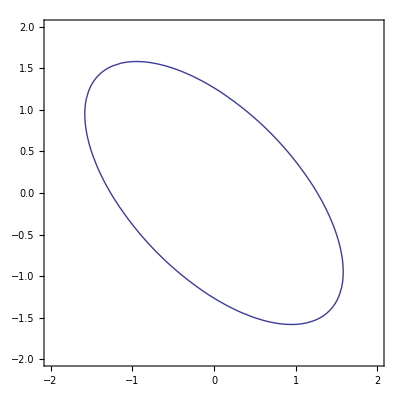

```mathematica
ContourPlot[(x/Sqrt[2]+y/Sqrt[2])^2+(-x/Sqrt[2]+y/Sqrt[2])^2/4==1,{x,-2,2},{y,-2,2}]
```

```mathematica
P=({{1, -1}, {1, 1}})
Dd=({{3, 0}, {0, -1}})
A=P. Dd. Inverse[P]
A//MatrixForm
A//Eigenvectors
```

{{1,-1},{1,1}}

{{3,0},{0,-1}}

{{1,2},{2,1}}

(1 | 2
2 | 1)

{{1,1},{-1,1}}